Evolution of intermediate excitons in fluid argon and krypton

```mathematica
ec = 1.602176634*10^-19 ; (*单位：库仑*)
em = 9.10938215*10^-28; (*单位：克*)
cgsec = ec  * 3*10^9;
```

```mathematica
cgs单位制系数计算：78.4K，24.8，单位 s-2
```

1944.32 ，^2 ： cgs单位制系数计算 K (-2+单位 s)

```mathematica
rho1 = 24.8*10^21;
c1 = (4*π*cgsec*cgsec * rho1)/em
```

7.9038×10^31

```mathematica
cgs单位制系数计算：86.8K，21.2
```

1840.16 ， ： cgs单位制系数计算 K

```mathematica
rho2 = 21.2*10^21;
c2 = (4*π*cgsec*cgsec * rho2)/em
```

6.75647×10^31

```mathematica
转换到eV （自然单位制？？）：
```

（ ） ： ？^2 自然单位制 转换到eV

```mathematica
hbar = 4.1356676969*10^-15/2/Pi;
```

```mathematica
c1m = c1 * hbar*hbar
```

34.2427

```mathematica
c2m = c2 * hbar *hbar
```

29.2719

Complex dielectric constant at 86.8K :

```mathematica
(*86.8K, 21.1density*)
epsilonr = 2.00;
rho = 21.1*10^21;
f1 = 0.398;
f3 = 0.28;
E1 = 11.73;
gamma1 = 0.14;
E3 = 11.95;
gamma3 = 0.15;
```

```mathematica
(*147.3K, 0.425density*)
epsilonr = 1.02
rho = 0.425*10^21;
f1 = 0.126;
f3 = 0.22;
E1 = 11.608;
gamma1 = 0.008;
E3 = 11.814;
gamma3 = 0.006;
```

1.02

```mathematica
epsilon[x_] := epsilonr + c2m*(f3/(E3^2-x*x-ⅈ*gamma3*x) + f1/(E1^2-x*x-ⅈ*gamma1*x))
```

```mathematica
epsilon[x_] := epsilonr + c2m*( f1/(E1^2-x*x-ⅈ*gamma1*x))
```

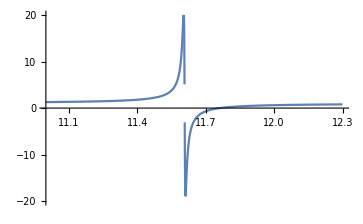

```mathematica
Plot[Re[epsilon[x]], {x, 11.0, 12.3}, AxesOrigin->{11.0, 0.0}, PlotRange->{-20, 20}]
```

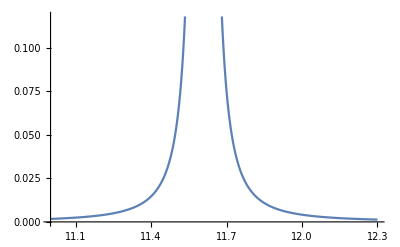

```mathematica
Plot[Im[epsilon[x]], {x, 11.0, 12.3}, AxesOrigin->{11.0, 0.0}]
```

```mathematica
epsilon1[x_] := Re[epsilon[x]]
epsilon2[x_]:= Im[epsilon[x]]
```

```mathematica
nindex[x_] := √((epsilon1[x] + √(epsilon1[x]^2+epsilon2[x]^2))/2)
```

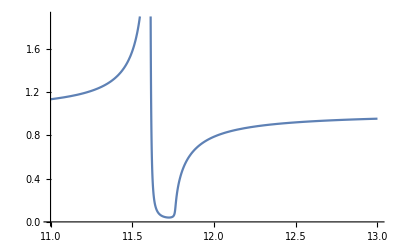

```mathematica
Plot[nindex[x], {x, 11.0, 13}]
```

```mathematica
kindex[x_]:=√((-epsilon1[x] + √(epsilon1[x]^2+epsilon2[x]^2))/2)
```

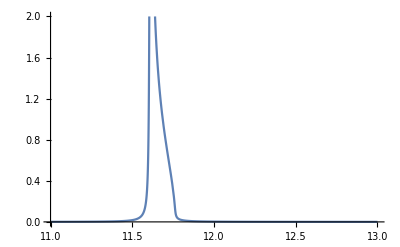

```mathematica
Plot[kindex[x], {x, 11.0, 13}, PlotRange->{{11, 13}, {0, 2}}]
```

```mathematica
nindex[1240./128];
```

```mathematica
ncomplex[x_] := nindex[x] + ⅈ*kindex[x]
```

```mathematica
nmToeV[x_] := 1240./x;
```

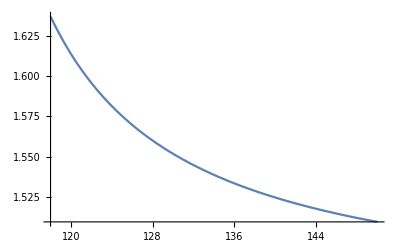

```mathematica
Plot[nindex[nmToeV[x]], {x, 118, 150}]
```

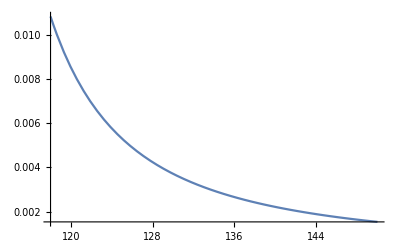

```mathematica
Plot[kindex[nmToeV[x]], {x, 118, 150}]
```

```mathematica
eVTonm[x_]:= 1240./x
eVTonm[11.73]
```

105.712

```mathematica
eVTonm[11.95]
```

103.766

Local field corrections:

```mathematica
epsilonr = 2.00;
rho = 21.1*10^21;
fa = 0.054;
fb = 0.207;
Ea = 11.79;
gamma1 = 0.14;
Eb = 12.05;
gamma3 = 0.15;
```

```mathematica
epsilonLF[x_]:=epsilonr + c2m*(fa/(Ea^2-x*x-ⅈ*gamma1*x) + fb/(Eb^2-x*x-ⅈ*gamma3*x));
epsilonLF1[x_] := Re[epsilonLF[x]]
epsilonLF2[x_]:= Im[epsilonLF[x]]
```

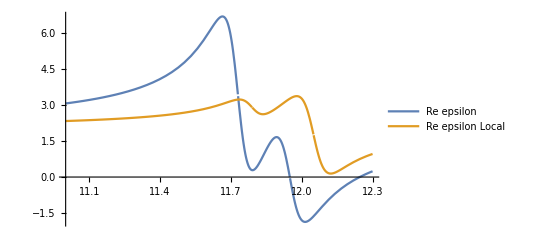

```mathematica
Plot[{epsilon1[x],epsilonLF1[x]}, {x, 11.0, 12.3}, AxesOrigin->{11.0, 0.0}, PlotLegends->{"Re epsilon", "Re epsilon  Local"}]
```

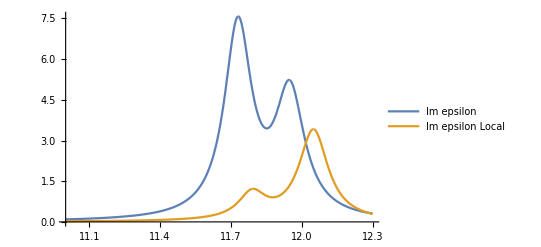

```mathematica
Plot[{epsilon2[x],epsilonLF2[x]}, {x, 11.0, 12.3}, AxesOrigin->{11.0, 0.0}, PlotLegends->{"Im epsilon", "Im epsilon  Local"}]
```

```mathematica
nindexLF[x_] := √((epsilonLF1[x] + √(epsilonLF1[x]^2+epsilonLF2[x]^2))/2)
```

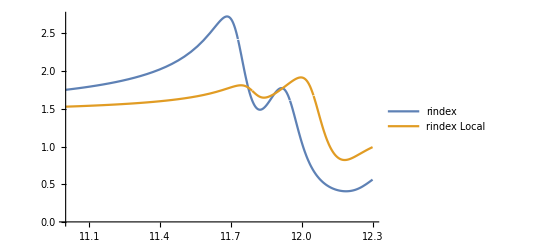

```mathematica
Plot[{nindex[x],nindexLF[x]}, {x, 11.0, 12.3}, AxesOrigin->{11.0, 0.0}, PlotLegends->{"rindex", "rindex Local"}]
```

Reflectivity:

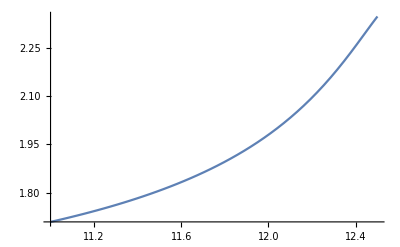

```mathematica
nrindexLiF[x_] := √(1+ 38*(12.8234*12.8234-x*x)/((12.8234*12.8234-x*x)*(12.8234*12.8234-x*x)+0.42357*0.42357*x*x) + 247.188/(18.8448*18.8448-x*x))
Plot[nrindexLiF[x], {x, 11, 12.5}]
```

```mathematica
rft[x_] := Abs[(ncomplex[x]-nrindexLiF[x])/(ncomplex[x]+nrindexLiF[x])]^2
```

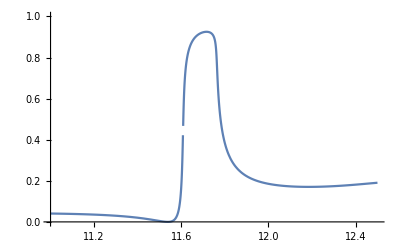

```mathematica
Plot[rft[x], {x, 11, 12.5}, PlotRange->{{11,12.5}, {0, 1}}]
```